# Manipulador Cartesiano: solución con perfil triangular y medio arco

Ubicación del centro respecto a {I}: {0.275,0.175,0.}

Radio del arco = 0.0790569

Longitud del arco =0.248365

Evolución del perfil

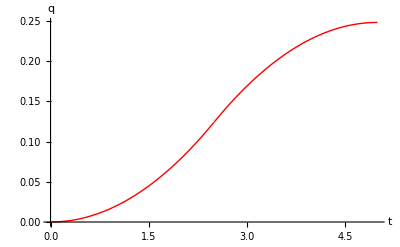

Velocidad del perfil

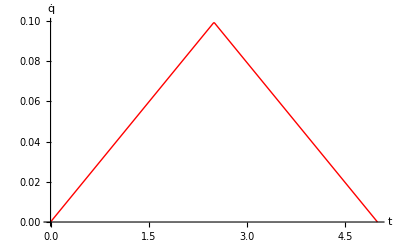

Aceleración del perfil

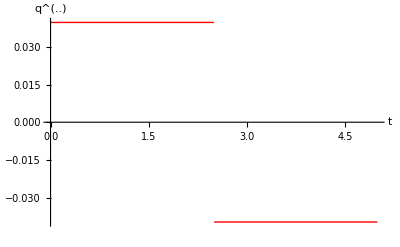

Evolución del arco

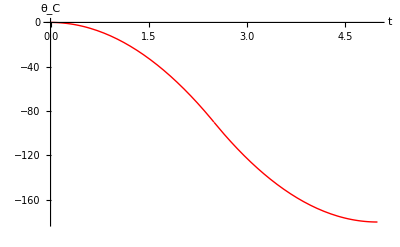

Vector (x̂)_c={0.316228,0.,-0.948683}

Vector (ẑ)_c={0,1,0}

Vector (ŷ)_c={-0.948683,0.,-0.316228}

^0R_C = {{0.316228,-0.948683,0},{0.,0.,1},{-0.948683,-0.316228,0}}

{-0.948683,0.316228,0.}

{-0.316228,-0.948683,0.}

{0,0,1}

En el sistema {I}, ^IR_C ={{-0.948683,-0.316228,0},{0.316228,-0.948683,0},{0.,0.,1}}

Evolución de las coordenadas del OT respecto a {I}

Recordar que x=d_1

Recordar que y=d_2

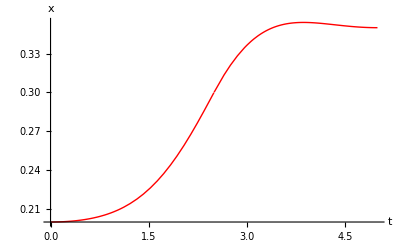

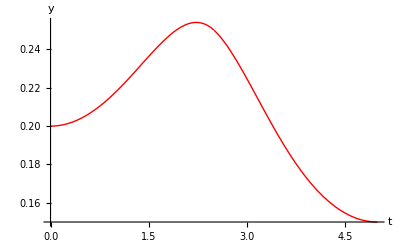

Derivadas articulares

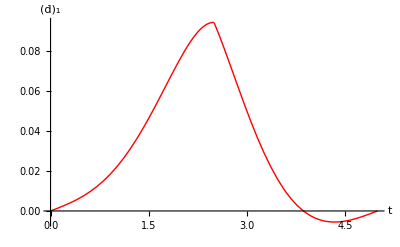

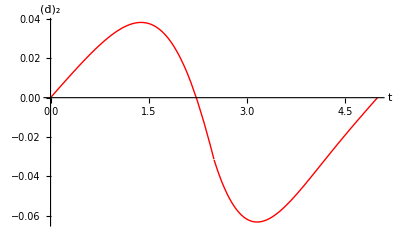

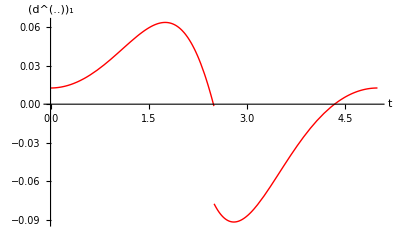

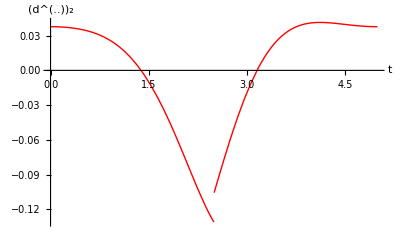

Gráficas de fuerzas

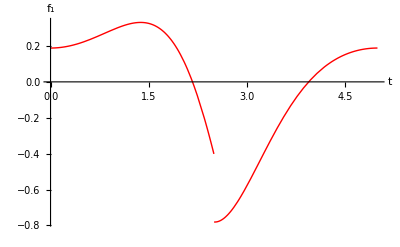

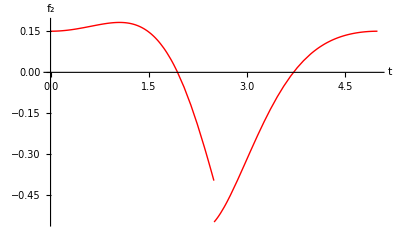

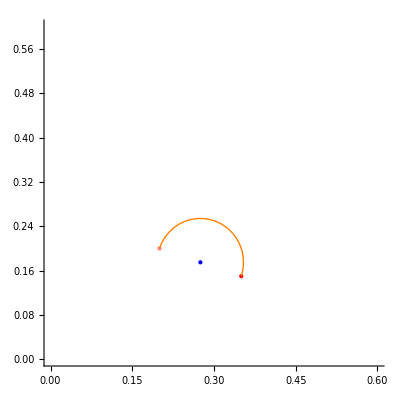

```mathematica
Clear[t,q]
(* Medidas de los eslabones *)
(* Se están despreciando las dimensiones y masas de los tornillos sin fin *)

a1=.10;
b1=.05;
c1=.05;
m[1]=2;

a2=.10;
b2=.05;
c2=.05;
m[2]=2;

(*Matriz de Rotación entre {0} y el marco inercial cuyo plano xy es paralelo con el piso {I} *)

RI0=({{0, 0, 1}, {1, 0, 0}, {0, 1, 0}});
(*Coordenadas de los puntos de inicio y fin respecto a {I}  *)
xI0=.20;
yI0=.20;
zI0=0;

xIf=.35;
yIf=.15;
zIf=0;
(* Posición inicial y final de la semicircunferencia respecto al marco {I} *)
P0I={xI0,yI0,zI0};
PfI={xIf,yIf,zIf};

(* Posición inicial respecto a {0}*)
P00=Transpose[RI0].{xI0,yI0,zI0};
(* Posición final  respecto a {0} *)
P0f=Transpose[RI0].{xIf,yIf,zIf};

(*Coordenadas del centro respecto a {0} *)
P0C={(P0f[[1]]+P00[[1]])/2,(P0f[[2]]+P00[[2]])/2,(P0f[[3]]+P00[[3]])/2};

PIC=RI0.P0C//N;
Print["Ubicación del centro respecto a {I}: ",PIC]
(*Obtención del radio*)
rc=Norm[P00-P0C];
Print["Radio del arco = ",rc]

(*Lugar geométrico: línea recta     *)
qf=π*rc//N;
Print["Longitud del arco =",qf]
(* Perfil de trayectoria: Triangular *)
tf=5;

q1=2 qf/tf^2 t^2;
q2=-2 qf/tf^2 t^2+4 qf/tf t-qf;

q=Piecewise[{{q1,t<tf/2},{q2,t≥tf/2}}];

Print["Evolución del perfil"]
Plot[q,{t,0,tf},AxesLabel->{"t","q"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Print["Velocidad del perfil"]
qp=D[q,t];
Plot[qp,{t,0,tf},AxesLabel->{"t","q̇"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Print["Aceleración del perfil"]
qpp=D[qp,t];
Plot[qpp,{t,0,tf},AxesLabel->{"t","q^(..)"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]

(* Parametrización del arco      *)
(* El signo menos es por el movimiento horario *)
θC=(-q/rc);
Print["Evolución del arco"]
Plot[θC*180/π,{t,0,tf},AxesLabel->{"t","θ_C"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]

(*Sistema de referencia ubicado en el Centro de la circunferencia*)
x0cu=(P00-P0C)/Norm[P00-P0C];
Print["Vector (x̂)_c=",x0cu]
z0cu={0,1,0};
Print["Vector (ẑ)_c=",z0cu]
y0cu=(z0cu×x0cu)/Norm[z0cu×x0cu];
Print["Vector (ŷ)_c=",y0cu]
(*Matriz de rotación del sistema del {C} respecto al sistema 0*)
R0C=({{x0cu[[1]], y0cu[[1]], z0cu[[1]]}, {x0cu[[2]], y0cu[[2]], z0cu[[2]]}, {x0cu[[3]], y0cu[[3]], z0cu[[3]]}});

Print[" ^0R_C = ",R0C]
(* Descripción de los vectores del sistema del centro del semiarco en términos 
del sistema {I]*)
xIcu=RI0.x0cu
yIcu=RI0.y0cu
zIcu=RI0.z0cu

RIC=({{xIcu[[1]], yIcu[[1]], zIcu[[1]]}, {xIcu[[2]], yIcu[[2]], zIcu[[2]]}, {xIcu[[3]], yIcu[[3]], zIcu[[3]]}});

Print["En el sistema {I}, ^IR_C =",RIC]

(*Parametrización de la curva*)
cx=rc Cos[θC];
cy=rc Sin[θC];
cz=0;
(*Vector de posición de cada punto del punto del arco respecto al centro*)
cP={cx,cy,cz};
(*Vector de posición del OT (órgano terminal) P respecto a {0}*)
P0T=P0C+R0C.cP;
Print["Evolución de las coordenadas del OT respecto a {I}"]
Print["Recordar que x=d_1"]
Print["Recordar que y=d_2"]
PIOT=RI0.P0T;

(* x,y medidos respecto a {I}  *)
x=PIOT[[1]];
y=PIOT[[2]];
Plot[x,{t,0,tf},AxesLabel->{"t","x"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[y,{t,0,tf},AxesLabel->{"t","y"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]

(*  Cinemática inversa   y           *)

d1=x;
d2=y;

(*Derivadas articulares*)

dp[1]=D[d1,t];
dp[2]=D[d2,t];
dpp[1]=D[dp[1],t];
dpp[2]=D[dp[2],t];

(* Fuerzas del motor 2 *)
Fm2=1.5*(dpp[1]+dpp[2])*m[2];

(* Fuerza del motor 1 *)
Fm1=1.5*(dpp[2]*m[2]+dpp[1]*(m[1]+m[2]));

Print["Derivadas articulares"]
Plot[dp[1],{t,0,tf},AxesLabel->{"t","(ḋ)_1"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[dp[2],{t,0,tf},AxesLabel->{"t","(ḋ)_2"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[dpp[1],{t,0,tf},AxesLabel->{"t","(d^(..))_1"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[dpp[2],{t,0,tf},AxesLabel->{"t","(d^(..))_2"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Print["Gráficas de fuerzas"]
Plot[Fm1,{t,0,tf},AxesLabel->{"t","f_1"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[Fm2,{t,0,tf},AxesLabel->{"t","f_2"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]

(*Dibujando el Manipulador*)

rango=PlotRange->{{0,.60},{0,.60}};
ejes=Axes->True;
aspecto=AspectRatio ->1/1;

curva=Circle[{PIC[[1]],PIC[[2]]},rc,{ArcTan[(yIf-yI0)/(xIf-xI0)]//N,π+ArcTan[(yIf-yI0)/(xIf-xI0)]//N}];
point0=Point[{xI0,yI0}];
pointf=Point[{xIf,yIf}];
pointc=Point[{PIC[[1]],PIC[[2]]}];
Graphics[{PointSize[Large],Pink,point0,PointSize[Large],Red,pointf,PointSize[Large],Blue,pointc,Orange,curva},
rango,
ejes,
aspecto
]
eslabon1=Line[{{0,0},{d1,0}}];
eslabon2=Line[{{d1,0},{x,y}}];
brazo={eslabon1,eslabon2};
imagen=Graphics[{Thick,Blue,brazo,PointSize[Large],Pink,point0,PointSize[Large],Red,pointf,PointSize[Large],Blue,pointc,Thick,Orange,curva},rango,ejes,aspecto];
(* Para hacer el paso más fino se recomienda un paso de 0.01 *)
tabla=Table[imagen,{t,0,tf,.01}];
ListAnimate[tabla]
```